```mathematica
Quit[]
```

```mathematica
bornDiagrams=4;
scriptIndex=1;
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
<<"/home/riccardo/Programs/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
SetProcess[{F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]}];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
userIntegralMasses[userIntegralFamiliesNames]
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/kinematics.m.

userIntegralMasses[{B0}]

## Diagrams generation

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish_var", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
topologiesBorn=CreateTopologies[0,2->2,ExcludeTopologies->Tadpoles];
fieldsBorn=InsertFields[topologiesBorn, process];
topologies1L=CreateTopologies[1,2-> 2,ExcludeTopologies->{Tadpoles,WFCorrections}];
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish_var.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish_var} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 43 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 49 Particles insertions

> Top. 13: 16 Particles insertions

> Top. 14: 20 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 34 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

> Top. 26: 0 Particles insertions

> Top. 27: 0 Particles insertions

> Top. 28: 0 Particles insertions

> Top. 29: 0 Particles insertions

> Top. 30: 0 Particles insertions

> Top. 31: 0 Particles insertions

> Top. 32: 0 Particles insertions

> Top. 33: 0 Particles insertions

> Top. 34: 0 Particles insertions

> Top. 35: 0 Particles insertions

> Top. 36: 0 Particles insertions

> Top. 37: 0 Particles insertions

> Top. 38: 0 Particles insertions

> Top. 39: 0 Particles insertions

> Top. 40: 214 Particles insertions

> Top. 41: 0 Particles insertions

> Top. 42: 0 Particles insertions

Restoring 24 field point(s)

in total: 376 Particles insertions

```mathematica
ampBorn=CreateFeynAmp[fieldsBorn,GaugeRules->{}];
amp1L=CreateFeynAmp[fields1L,GaugeRules->{}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 43 Particles amplitudes

> Top. 2: 49 Particles amplitudes

> Top. 3: 16 Particles amplitudes

> Top. 4: 20 Particles amplitudes

> Top. 5: 34 Particles amplitudes

> Top. 6: 214 Particles amplitudes

in total: 376 Particles amplitudes

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

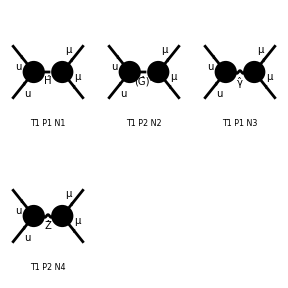

```mathematica
Paint[fieldsBorn];
```

```mathematica
myAmpBorn=ExtractAmplitude[ampBorn];
myAmp1L=ExtractAmplitude[amp1L];
```

```mathematica
SaveAmplitudes[myAmpBorn,"BornAmplitudes.m"];
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/feynArts_amplitudes/BornAmplitudes.m

$Aborted

```mathematica
myAmpBorn[[2]]
```

-v̄[p2,MU].(EL gXuu MU om_--EL gXuu MU om_+).u[p1,MU] ū[k1,MM].(-EL gXll MM om_-+EL gXll MM om_+).v[k2,MM] 1/((k1+k2)^2-MZ^2 xi_bg)

```mathematica
AmpSquare[myAmpBorn[[2]],myAmpBorn[[2]]]
```

(EL^4 gXll^2 gXuu^2 mm^2 mu^2 s (2 mm^2+2 mu^2+s))/((s-mz^2 xi_bg)^2)

```mathematica
gXll/.parameterReplace
```

1/(2 mw sw)

```mathematica
gXuu/.parameterReplace
```

1/(2 mw sw)

## Interference

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/kinematics.m.

### Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
```

```mathematica
smBorn=Sum[AmpSquare[myAmpBorn[[i]],myAmpBorn[[j]]],{i,1,Length[myAmpBorn]},{j,1,Length[myAmpBorn]}];
```

```mathematica
smBorn/.parameterReplace/.{I3l1->-1/2,Ql1->-1}//Simplify
```

1/64 EL^4 ((4 me^2 mm^2 (2 me^2-s) (4 mm^2-s))/(mw^4 (mh^2-s)^2 sw^4)+(16 I3l2 me^2 mm^2 s)/(cw^2 mw^2 (mz^2-s)^2 sw^4)-(128 me^2 mm^2 Ql2 (2 mm^2-s-2 t))/(mw^2 (mh^2-s) s sw^2)+(32 me^2 mm^2 (1/2-2 sw^2) (I3l2-2 Ql2 sw^2) (2 mm^2-s-2 t))/(cw^2 mw^2 (mh^2-s) (mz^2-s) sw^4)+(64 Ql2^2 (4 mm^4-2 s^2+d s^2+2 me^2 (4 mm^2+(-2+d) s)-8 mm^2 t+4 s t+4 t^2))/s^2-1/(cw^2 (mz^2-s) s sw^2)16 Ql2 (2 Ql2 sw^2 (-1+4 sw^2) (4 mm^4-2 s^2+d s^2+2 me^2 (4 mm^2+(-2+d) s)-8 mm^2 t+4 s t+4 t^2)+I3l2 (4 s^2-4 d s^2+d^2 s^2+8 s^2 sw^2-4 d s^2 sw^2+mm^4 (4-16 sw^2)-2 me^2 (4 mm^2+(-2+d) s) (-1+4 sw^2)+16 s t-10 d s t+2 d^2 s t-16 s sw^2 t+4 t^2-16 sw^2 t^2-2 mm^2 ((6-5 d+d^2) s+4 (1-4 sw^2) t)))+1/(cw^4 (mz^2-s)^2 sw^4)16 (8 d me^2 mm^2 Ql2 sw^4 (-1+2 sw^2) (-I3l2+Ql2 sw^2)+mm^4 (1-4 sw^2+8 sw^4) (I3l2^2-2 I3l2 Ql2 sw^2+2 Ql2^2 sw^4)+1/4 (-2+d) s^2 (2 Ql2^2 sw^4 (1-4 sw^2+8 sw^4)+I3l2^2 (-2+d+8 sw^2-4 d sw^2+8 sw^4)-2 I3l2 Ql2 sw^2 (-2+d+8 sw^2-4 d sw^2+8 sw^4))+(1-4 sw^2+8 sw^4) (I3l2^2-2 I3l2 Ql2 sw^2+2 Ql2^2 sw^4) t^2+2 s (2 (2-d) sw^2 (mm^2 Ql2 (I3l2-Ql2 sw^2) (1/4-sw^2+2 sw^4)+me^2 (1/2-sw^2) (Ql2^2 sw^4+(I3l2-Ql2 sw^2)^2))+(-(4-5 d+d^2) I3l2^2 sw^4+2 (4-5 d+d^2) I3l2 Ql2 sw^6+4 Ql2^2 sw^8+1/4 (1-2 sw^2)^2 ((8-5 d+d^2) I3l2^2-2 (8-5 d+d^2) I3l2 Ql2 sw^2+4 Ql2^2 sw^4)) t)+2 mm^2 (1/4 (-2+d) s (-2 Ql2^2 sw^4 (1-4 sw^2+8 sw^4)-I3l2^2 (-2+d+8 sw^2-4 d sw^2+8 sw^4)+2 I3l2 Ql2 sw^2 (-2+d+8 sw^2-4 d sw^2+8 sw^4))-(Ql2^2 sw^4+(I3l2-Ql2 sw^2)^2) (2 (-2+d) me^2 sw^2 (-1+2 sw^2)+(1-4 sw^2+8 sw^4) t)))+(me^2 mm^2 (2 s+mm^2 (-4+ABISS`Private`GTr[])) (2 s+me^2 ABISS`Private`GTr[]))/(mw^4 (mz^2-s)^2 sw^4))

```mathematica
myAmpBorn[[2]]
```

-v̄[p2,ME].(-EL gXll ME om_-+EL gXll ME om_+).u[p1,ME] ū[k1,MM].(-EL gXll MM om_-+EL gXll MM om_+).v[k2,MM] 1/(-MZ^2+(k1+k2)^2)

```mathematica
AmpSquare[myAmpBorn[[2]],myAmpBorn[[2]]]
```

(EL^4 gXll^4 me^2 mm^2 (2 s+me^2 ABISS`Private`GTr[]) (-4 mm^2+2 s+mm^2 ABISS`Private`GTr[]))/(4 (mz^2-s)^2)

```mathematica
SquareSimplifyAndSave[myAmp1L,myAmpBorn];
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_1_1.m.

ABISS: Computed contribution 1-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_1_2.m.

ABISS: Computed contribution 1-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_1_3.m.

ABISS: Computed contribution 1-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_1_4.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_2_1.m.

ABISS: Computed contribution 2-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_2_2.m.

ABISS: Computed contribution 2-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_2_3.m.

ABISS: Computed contribution 2-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_2_4.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_3_1.m.

ABISS: Computed contribution 3-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_3_2.m.

ABISS: Computed contribution 3-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_3_3.m.

ABISS: Computed contribution 3-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_3_4.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_4_1.m.

ABISS: Computed contribution 4-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_4_2.m.

ABISS: Computed contribution 4-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_4_3.m.

ABISS: Computed contribution 4-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_4_4.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_5_1.m.

ABISS: Computed contribution 5-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_5_2.m.

ABISS: Computed contribution 5-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_5_3.m.

ABISS: Computed contribution 5-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_5_4.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_6_1.m.

ABISS: Computed contribution 6-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_6_2.m.

ABISS: Computed contribution 6-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_6_3.m.

ABISS: Computed contribution 6-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_6_4.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_7_1.m.

ABISS: Computed contribution 7-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_7_2.m.

ABISS: Computed contribution 7-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_7_3.m.

ABISS: Computed contribution 7-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_7_4.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_8_1.m.

ABISS: Computed contribution 8-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_8_2.m.

ABISS: Computed contribution 8-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_8_3.m.

ABISS: Computed contribution 8-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_8_4.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_9_1.m.

ABISS: Computed contribution 9-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_9_2.m.

ABISS: Computed contribution 9-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_9_3.m.

ABISS: Computed contribution 9-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_9_4.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_10_1.m.

ABISS: Computed contribution 10-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_10_2.m.

ABISS: Computed contribution 10-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_10_3.m.

ABISS: Computed contribution 10-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_10_4.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_11_1.m.

ABISS: Computed contribution 11-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_11_2.m.

ABISS: Computed contribution 11-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_11_3.m.

ABISS: Computed contribution 11-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_11_4.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_12_1.m.

ABISS: Computed contribution 12-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_12_2.m.

ABISS: Computed contribution 12-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_12_3.m.

ABISS: Computed contribution 12-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_12_4.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_13_1.m.

ABISS: Computed contribution 13-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_13_2.m.

ABISS: Computed contribution 13-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_13_3.m.

ABISS: Computed contribution 13-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_13_4.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_14_1.m.

ABISS: Computed contribution 14-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_14_2.m.

ABISS: Computed contribution 14-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_14_3.m.

ABISS: Computed contribution 14-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_14_4.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_15_1.m.

ABISS: Computed contribution 15-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_15_2.m.

ABISS: Computed contribution 15-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_15_3.m.

ABISS: Computed contribution 15-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_15_4.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_16_1.m.

ABISS: Computed contribution 16-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_16_2.m.

ABISS: Computed contribution 16-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_16_3.m.

ABISS: Computed contribution 16-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_16_4.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_17_1.m.

ABISS: Computed contribution 17-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_17_2.m.

ABISS: Computed contribution 17-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_17_3.m.

ABISS: Computed contribution 17-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_17_4.m.

ABISS: Computed contribution 18-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_18_1.m.

ABISS: Computed contribution 18-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_18_2.m.

ABISS: Computed contribution 18-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_18_3.m.

ABISS: Computed contribution 18-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_18_4.m.

ABISS: Computed contribution 19-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_19_1.m.

ABISS: Computed contribution 19-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_19_2.m.

ABISS: Computed contribution 19-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_19_3.m.

ABISS: Computed contribution 19-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_19_4.m.

ABISS: Computed contribution 20-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_20_1.m.

ABISS: Computed contribution 20-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_20_2.m.

ABISS: Computed contribution 20-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_20_3.m.

ABISS: Computed contribution 20-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_20_4.m.

ABISS: Computed contribution 21-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_21_1.m.

ABISS: Computed contribution 21-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_21_2.m.

ABISS: Computed contribution 21-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_21_3.m.

ABISS: Computed contribution 21-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_21_4.m.

ABISS: Computed contribution 22-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_22_1.m.

ABISS: Computed contribution 22-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_22_2.m.

ABISS: Computed contribution 22-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_22_3.m.

ABISS: Computed contribution 22-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_22_4.m.

ABISS: Computed contribution 23-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_23_1.m.

ABISS: Computed contribution 23-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_23_2.m.

ABISS: Computed contribution 23-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_23_3.m.

ABISS: Computed contribution 23-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_23_4.m.

ABISS: Computed contribution 24-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_24_1.m.

ABISS: Computed contribution 24-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_24_2.m.

ABISS: Computed contribution 24-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_24_3.m.

ABISS: Computed contribution 24-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_24_4.m.

ABISS: Computed contribution 25-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_25_1.m.

ABISS: Computed contribution 25-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_25_2.m.

ABISS: Computed contribution 25-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_25_3.m.

ABISS: Computed contribution 25-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_25_4.m.

ABISS: Computed contribution 26-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_26_1.m.

ABISS: Computed contribution 26-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_26_2.m.

ABISS: Computed contribution 26-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_26_3.m.

ABISS: Computed contribution 26-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_26_4.m.

ABISS: Computed contribution 27-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_27_1.m.

ABISS: Computed contribution 27-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_27_2.m.

ABISS: Computed contribution 27-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_27_3.m.

ABISS: Computed contribution 27-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_27_4.m.

ABISS: Computed contribution 28-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_28_1.m.

ABISS: Computed contribution 28-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_28_2.m.

ABISS: Computed contribution 28-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_28_3.m.

ABISS: Computed contribution 28-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_28_4.m.

ABISS: Computed contribution 29-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_29_1.m.

ABISS: Computed contribution 29-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_29_2.m.

ABISS: Computed contribution 29-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_29_3.m.

ABISS: Computed contribution 29-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_29_4.m.

ABISS: Computed contribution 30-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_30_1.m.

ABISS: Computed contribution 30-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_30_2.m.

ABISS: Computed contribution 30-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_30_3.m.

ABISS: Computed contribution 30-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_30_4.m.

ABISS: Computed contribution 31-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_31_1.m.

ABISS: Computed contribution 31-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_31_2.m.

ABISS: Computed contribution 31-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_31_3.m.

ABISS: Computed contribution 31-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_31_4.m.

ABISS: Computed contribution 32-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_32_1.m.

ABISS: Computed contribution 32-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_32_2.m.

ABISS: Computed contribution 32-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_32_3.m.

ABISS: Computed contribution 32-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_32_4.m.

ABISS: Computed contribution 33-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_33_1.m.

ABISS: Computed contribution 33-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_33_2.m.

ABISS: Computed contribution 33-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_33_3.m.

ABISS: Computed contribution 33-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_33_4.m.

ABISS: Computed contribution 34-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_34_1.m.

ABISS: Computed contribution 34-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_34_2.m.

ABISS: Computed contribution 34-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_34_3.m.

ABISS: Computed contribution 34-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_34_4.m.

ABISS: Computed contribution 35-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_35_1.m.

ABISS: Computed contribution 35-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_35_2.m.

ABISS: Computed contribution 35-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_35_3.m.

ABISS: Computed contribution 35-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_35_4.m.

ABISS: Computed contribution 36-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_36_1.m.

ABISS: Computed contribution 36-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_36_2.m.

ABISS: Computed contribution 36-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_36_3.m.

ABISS: Computed contribution 36-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_36_4.m.

ABISS: Computed contribution 37-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_37_1.m.

ABISS: Computed contribution 37-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_37_2.m.

ABISS: Computed contribution 37-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_37_3.m.

ABISS: Computed contribution 37-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_37_4.m.

ABISS: Computed contribution 38-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_38_1.m.

ABISS: Computed contribution 38-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_38_2.m.

ABISS: Computed contribution 38-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_38_3.m.

ABISS: Computed contribution 38-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_38_4.m.

ABISS: Computed contribution 39-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_39_1.m.

ABISS: Computed contribution 39-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_39_2.m.

ABISS: Computed contribution 39-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_39_3.m.

ABISS: Computed contribution 39-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_39_4.m.

ABISS: Computed contribution 40-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_40_1.m.

ABISS: Computed contribution 40-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_40_2.m.

ABISS: Computed contribution 40-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_40_3.m.

ABISS: Computed contribution 40-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_40_4.m.

ABISS: Computed contribution 41-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_41_1.m.

ABISS: Computed contribution 41-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_41_2.m.

ABISS: Computed contribution 41-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_41_3.m.

ABISS: Computed contribution 41-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_41_4.m.

ABISS: Computed contribution 42-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_42_1.m.

ABISS: Computed contribution 42-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_42_2.m.

ABISS: Computed contribution 42-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_42_3.m.

ABISS: Computed contribution 42-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_42_4.m.

ABISS: Computed contribution 43-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_43_1.m.

ABISS: Computed contribution 43-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_43_2.m.

ABISS: Computed contribution 43-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_43_3.m.

ABISS: Computed contribution 43-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_43_4.m.

ABISS: Computed contribution 44-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_44_1.m.

ABISS: Computed contribution 44-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_44_2.m.

ABISS: Computed contribution 44-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_44_3.m.

ABISS: Computed contribution 44-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_44_4.m.

ABISS: Computed contribution 45-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_45_1.m.

ABISS: Computed contribution 45-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_45_2.m.

ABISS: Computed contribution 45-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_45_3.m.

ABISS: Computed contribution 45-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_45_4.m.

ABISS: Computed contribution 46-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_46_1.m.

ABISS: Computed contribution 46-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_46_2.m.

ABISS: Computed contribution 46-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_46_3.m.

ABISS: Computed contribution 46-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_46_4.m.

ABISS: Computed contribution 47-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_47_1.m.

ABISS: Computed contribution 47-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_47_2.m.

ABISS: Computed contribution 47-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_47_3.m.

ABISS: Computed contribution 47-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_47_4.m.

ABISS: Computed contribution 48-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_48_1.m.

ABISS: Computed contribution 48-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_48_2.m.

ABISS: Computed contribution 48-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_48_3.m.

ABISS: Computed contribution 48-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_48_4.m.

ABISS: Computed contribution 49-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_49_1.m.

ABISS: Computed contribution 49-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_49_2.m.

ABISS: Computed contribution 49-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_49_3.m.

ABISS: Computed contribution 49-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_49_4.m.

ABISS: Computed contribution 50-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_50_1.m.

ABISS: Computed contribution 50-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_50_2.m.

ABISS: Computed contribution 50-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_50_3.m.

ABISS: Computed contribution 50-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_50_4.m.

ABISS: Computed contribution 51-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_51_1.m.

ABISS: Computed contribution 51-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_51_2.m.

ABISS: Computed contribution 51-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_51_3.m.

ABISS: Computed contribution 51-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_51_4.m.

ABISS: Computed contribution 52-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_52_1.m.

ABISS: Computed contribution 52-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_52_2.m.

ABISS: Computed contribution 52-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_52_3.m.

ABISS: Computed contribution 52-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_52_4.m.

ABISS: Computed contribution 53-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_53_1.m.

ABISS: Computed contribution 53-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_53_2.m.

ABISS: Computed contribution 53-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_53_3.m.

ABISS: Computed contribution 53-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_53_4.m.

ABISS: Computed contribution 54-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_54_1.m.

ABISS: Computed contribution 54-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_54_2.m.

ABISS: Computed contribution 54-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_54_3.m.

ABISS: Computed contribution 54-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_54_4.m.

ABISS: Computed contribution 55-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_55_1.m.

ABISS: Computed contribution 55-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_55_2.m.

ABISS: Computed contribution 55-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_55_3.m.

ABISS: Computed contribution 55-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_55_4.m.

ABISS: Computed contribution 56-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_56_1.m.

ABISS: Computed contribution 56-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_56_2.m.

ABISS: Computed contribution 56-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_56_3.m.

ABISS: Computed contribution 56-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_56_4.m.

ABISS: Computed contribution 57-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_57_1.m.

ABISS: Computed contribution 57-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_57_2.m.

ABISS: Computed contribution 57-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_57_3.m.

ABISS: Computed contribution 57-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_57_4.m.

ABISS: Computed contribution 58-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_58_1.m.

ABISS: Computed contribution 58-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_58_2.m.

ABISS: Computed contribution 58-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_58_3.m.

ABISS: Computed contribution 58-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_58_4.m.

ABISS: Computed contribution 59-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_59_1.m.

ABISS: Computed contribution 59-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_59_2.m.

ABISS: Computed contribution 59-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_59_3.m.

ABISS: Computed contribution 59-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_59_4.m.

ABISS: Computed contribution 60-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_60_1.m.

ABISS: Computed contribution 60-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_60_2.m.

ABISS: Computed contribution 60-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_60_3.m.

ABISS: Computed contribution 60-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_60_4.m.

ABISS: Computed contribution 61-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_61_1.m.

ABISS: Computed contribution 61-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_61_2.m.

ABISS: Computed contribution 61-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_61_3.m.

ABISS: Computed contribution 61-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_61_4.m.

ABISS: Computed contribution 62-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_62_1.m.

ABISS: Computed contribution 62-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_62_2.m.

ABISS: Computed contribution 62-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_62_3.m.

ABISS: Computed contribution 62-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_62_4.m.

ABISS: Computed contribution 63-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_63_1.m.

ABISS: Computed contribution 63-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_63_2.m.

ABISS: Computed contribution 63-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_63_3.m.

ABISS: Computed contribution 63-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_63_4.m.

ABISS: Computed contribution 64-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_64_1.m.

ABISS: Computed contribution 64-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_64_2.m.

ABISS: Computed contribution 64-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_64_3.m.

ABISS: Computed contribution 64-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_64_4.m.

ABISS: Computed contribution 65-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_65_1.m.

ABISS: Computed contribution 65-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_65_2.m.

ABISS: Computed contribution 65-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_65_3.m.

ABISS: Computed contribution 65-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_65_4.m.

ABISS: Computed contribution 66-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_66_1.m.

ABISS: Computed contribution 66-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_66_2.m.

ABISS: Computed contribution 66-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_66_3.m.

ABISS: Computed contribution 66-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_66_4.m.

ABISS: Computed contribution 67-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_67_1.m.

ABISS: Computed contribution 67-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_67_2.m.

ABISS: Computed contribution 67-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_67_3.m.

ABISS: Computed contribution 67-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_67_4.m.

ABISS: Computed contribution 68-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_68_1.m.

ABISS: Computed contribution 68-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_68_2.m.

ABISS: Computed contribution 68-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_68_3.m.

ABISS: Computed contribution 68-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_68_4.m.

ABISS: Computed contribution 69-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_69_1.m.

ABISS: Computed contribution 69-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_69_2.m.

ABISS: Computed contribution 69-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_69_3.m.

ABISS: Computed contribution 69-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_69_4.m.

ABISS: Computed contribution 70-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_70_1.m.

ABISS: Computed contribution 70-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_70_2.m.

ABISS: Computed contribution 70-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_70_3.m.

ABISS: Computed contribution 70-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_70_4.m.

ABISS: Computed contribution 71-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_71_1.m.

ABISS: Computed contribution 71-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_71_2.m.

ABISS: Computed contribution 71-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_71_3.m.

ABISS: Computed contribution 71-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_71_4.m.

ABISS: Computed contribution 72-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_72_1.m.

ABISS: Computed contribution 72-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_72_2.m.

ABISS: Computed contribution 72-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_72_3.m.

ABISS: Computed contribution 72-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_72_4.m.

ABISS: Computed contribution 73-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_73_1.m.

ABISS: Computed contribution 73-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_73_2.m.

ABISS: Computed contribution 73-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_73_3.m.

ABISS: Computed contribution 73-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_73_4.m.

ABISS: Computed contribution 74-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_74_1.m.

ABISS: Computed contribution 74-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_74_2.m.

ABISS: Computed contribution 74-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_74_3.m.

ABISS: Computed contribution 74-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_74_4.m.

ABISS: Computed contribution 75-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_75_1.m.

ABISS: Computed contribution 75-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_75_2.m.

ABISS: Computed contribution 75-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_75_3.m.

ABISS: Computed contribution 75-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_75_4.m.

ABISS: Computed contribution 76-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_76_1.m.

ABISS: Computed contribution 76-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_76_2.m.

ABISS: Computed contribution 76-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_76_3.m.

ABISS: Computed contribution 76-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_76_4.m.

ABISS: Computed contribution 77-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_77_1.m.

ABISS: Computed contribution 77-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_77_2.m.

ABISS: Computed contribution 77-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_77_3.m.

ABISS: Computed contribution 77-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_77_4.m.

ABISS: Computed contribution 78-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_78_1.m.

ABISS: Computed contribution 78-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_78_2.m.

ABISS: Computed contribution 78-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_78_3.m.

ABISS: Computed contribution 78-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_78_4.m.

ABISS: Computed contribution 79-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_79_1.m.

ABISS: Computed contribution 79-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_79_2.m.

ABISS: Computed contribution 79-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_79_3.m.

ABISS: Computed contribution 79-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_79_4.m.

ABISS: Computed contribution 80-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_80_1.m.

ABISS: Computed contribution 80-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_80_2.m.

ABISS: Computed contribution 80-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_80_3.m.

ABISS: Computed contribution 80-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_80_4.m.

ABISS: Computed contribution 81-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_81_1.m.

ABISS: Computed contribution 81-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_81_2.m.

ABISS: Computed contribution 81-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_81_3.m.

ABISS: Computed contribution 81-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_81_4.m.

ABISS: Computed contribution 82-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_82_1.m.

ABISS: Computed contribution 82-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_82_2.m.

ABISS: Computed contribution 82-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_82_3.m.

ABISS: Computed contribution 82-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_82_4.m.

ABISS: Computed contribution 83-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_83_1.m.

ABISS: Computed contribution 83-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_83_2.m.

ABISS: Computed contribution 83-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_83_3.m.

ABISS: Computed contribution 83-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_83_4.m.

ABISS: Computed contribution 84-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_84_1.m.

ABISS: Computed contribution 84-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_84_2.m.

ABISS: Computed contribution 84-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_84_3.m.

ABISS: Computed contribution 84-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_84_4.m.

ABISS: Computed contribution 85-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_85_1.m.

ABISS: Computed contribution 85-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_85_2.m.

ABISS: Computed contribution 85-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_85_3.m.

ABISS: Computed contribution 85-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_85_4.m.

ABISS: Computed contribution 86-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_86_1.m.

ABISS: Computed contribution 86-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_86_2.m.

ABISS: Computed contribution 86-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_86_3.m.

ABISS: Computed contribution 86-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_86_4.m.

ABISS: Computed contribution 87-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_87_1.m.

ABISS: Computed contribution 87-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_87_2.m.

ABISS: Computed contribution 87-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_87_3.m.

ABISS: Computed contribution 87-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_87_4.m.

ABISS: Computed contribution 88-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_88_1.m.

ABISS: Computed contribution 88-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_88_2.m.

ABISS: Computed contribution 88-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_88_3.m.

ABISS: Computed contribution 88-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_88_4.m.

ABISS: Computed contribution 89-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_89_1.m.

ABISS: Computed contribution 89-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_89_2.m.

ABISS: Computed contribution 89-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_89_3.m.

ABISS: Computed contribution 89-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_89_4.m.

ABISS: Computed contribution 90-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_90_1.m.

ABISS: Computed contribution 90-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_90_2.m.

ABISS: Computed contribution 90-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_90_3.m.

ABISS: Computed contribution 90-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_90_4.m.

ABISS: Computed contribution 91-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_91_1.m.

ABISS: Computed contribution 91-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_91_2.m.

ABISS: Computed contribution 91-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_91_3.m.

ABISS: Computed contribution 91-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_91_4.m.

ABISS: Computed contribution 92-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_92_1.m.

ABISS: Computed contribution 92-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_92_2.m.

ABISS: Computed contribution 92-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_92_3.m.

ABISS: Computed contribution 92-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_92_4.m.

ABISS: Computed contribution 93-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_93_1.m.

ABISS: Computed contribution 93-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_93_2.m.

ABISS: Computed contribution 93-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_93_3.m.

ABISS: Computed contribution 93-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_93_4.m.

ABISS: Computed contribution 94-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_94_1.m.

ABISS: Computed contribution 94-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_94_2.m.

ABISS: Computed contribution 94-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_94_3.m.

ABISS: Computed contribution 94-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_94_4.m.

ABISS: Computed contribution 95-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_95_1.m.

ABISS: Computed contribution 95-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_95_2.m.

ABISS: Computed contribution 95-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_95_3.m.

ABISS: Computed contribution 95-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_95_4.m.

ABISS: Computed contribution 96-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_96_1.m.

ABISS: Computed contribution 96-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_96_2.m.

ABISS: Computed contribution 96-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_96_3.m.

ABISS: Computed contribution 96-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_96_4.m.

ABISS: Computed contribution 97-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_97_1.m.

ABISS: Computed contribution 97-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_97_2.m.

ABISS: Computed contribution 97-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_97_3.m.

ABISS: Computed contribution 97-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_97_4.m.

ABISS: Computed contribution 98-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_98_1.m.

ABISS: Computed contribution 98-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_98_2.m.

ABISS: Computed contribution 98-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_98_3.m.

ABISS: Computed contribution 98-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_98_4.m.

ABISS: Computed contribution 99-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_99_1.m.

ABISS: Computed contribution 99-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_99_2.m.

ABISS: Computed contribution 99-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_99_3.m.

ABISS: Computed contribution 99-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_99_4.m.

ABISS: Computed contribution 100-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_100_1.m.

ABISS: Computed contribution 100-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_100_2.m.

ABISS: Computed contribution 100-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_100_3.m.

ABISS: Computed contribution 100-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_100_4.m.

ABISS: Computed contribution 101-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_101_1.m.

ABISS: Computed contribution 101-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_101_2.m.

ABISS: Computed contribution 101-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_101_3.m.

ABISS: Computed contribution 101-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_101_4.m.

ABISS: Computed contribution 102-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_102_1.m.

ABISS: Computed contribution 102-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_102_2.m.

ABISS: Computed contribution 102-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_102_3.m.

ABISS: Computed contribution 102-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_102_4.m.

ABISS: Computed contribution 103-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_103_1.m.

ABISS: Computed contribution 103-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_103_2.m.

ABISS: Computed contribution 103-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_103_3.m.

ABISS: Computed contribution 103-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_103_4.m.

ABISS: Computed contribution 104-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_104_1.m.

ABISS: Computed contribution 104-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_104_2.m.

ABISS: Computed contribution 104-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_104_3.m.

ABISS: Computed contribution 104-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_104_4.m.

ABISS: Computed contribution 105-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_105_1.m.

ABISS: Computed contribution 105-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_105_2.m.

ABISS: Computed contribution 105-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_105_3.m.

ABISS: Computed contribution 105-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_105_4.m.

ABISS: Computed contribution 106-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_106_1.m.

ABISS: Computed contribution 106-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_106_2.m.

ABISS: Computed contribution 106-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_106_3.m.

ABISS: Computed contribution 106-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_106_4.m.

ABISS: Computed contribution 107-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_107_1.m.

ABISS: Computed contribution 107-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_107_2.m.

ABISS: Computed contribution 107-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_107_3.m.

ABISS: Computed contribution 107-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_107_4.m.

ABISS: Computed contribution 108-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_108_1.m.

ABISS: Computed contribution 108-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_108_2.m.

ABISS: Computed contribution 108-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_108_3.m.

ABISS: Computed contribution 108-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_108_4.m.

ABISS: Computed contribution 109-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_109_1.m.

ABISS: Computed contribution 109-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_109_2.m.

ABISS: Computed contribution 109-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_109_3.m.

ABISS: Computed contribution 109-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_109_4.m.

ABISS: Computed contribution 110-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_110_1.m.

ABISS: Computed contribution 110-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_110_2.m.

ABISS: Computed contribution 110-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_110_3.m.

ABISS: Computed contribution 110-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_110_4.m.

ABISS: Computed contribution 111-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_111_1.m.

ABISS: Computed contribution 111-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_111_2.m.

ABISS: Computed contribution 111-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_111_3.m.

ABISS: Computed contribution 111-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_111_4.m.

ABISS: Computed contribution 112-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_112_1.m.

ABISS: Computed contribution 112-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_112_2.m.

ABISS: Computed contribution 112-3.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_112_3.m.

ABISS: Computed contribution 112-4.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_112_4.m.

ABISS: Computed contribution 113-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/qq-mm_1L//interferences/Contribution_113_1.m.

$Aborted

## Shift

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,370},{j,4}]
```

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,14},{j,1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_14_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,0,1,0],userIntegral[A0,{mh,mm},1,1,1,-1],userIntegral[A0,{mh,mm},1,-1,1,0],userIntegral[A0,{mh,mm},1,0,1,-1],userIntegral[A0,{mh,mm},1,1,1,-2],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mh,mm},1,1,0,-1],userIntegral[A0,{mh,mm},1,1,-1,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,0,1,0],userIntegral[A0,{mh,mm},0,1,1,-1],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},-1,1,1,0],userIntegral[A0,{mz,mm},1,-1,1,0],userIntegral[A0,{mz,mm},1,0,1,-1],userIntegral[A0,{mz,mm},1,0,1,0],userIntegral[A0,{mz,mm},1,1,1,-2],userIntegral[A0,{mz,mm},1,1,1,-1],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,-1],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,1,-1,0],userIntegral[A0,{mz,mm},0,0,1,0],userIntegral[A0,{mz,mm},0,1,1,-1],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},-1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[C0,{mw},1,0,1,0],userIntegral[C0,{mw},1,1,1,-1],userIntegral[C0,{mw},1,-1,1,0],userIntegral[C0,{mw},1,0,1,-1],userIntegral[C0,{mw},1,1,1,-2],userIntegral[C0,{mw},1,1,0,0],userIntegral[C0,{mw},1,0,0,0],userIntegral[C0,{mw},1,1,0,-1],userIntegral[C0,{mw},1,1,-1,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[C0,{mw},0,0,1,0],userIntegral[C0,{mw},0,1,1,-1],userIntegral[C0,{mw},0,1,0,0],userIntegral[C0,{mw},-1,1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[D0,{mm,mh,mz},1,-1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,-2],userIntegral[D0,{mm,mh,mz},1,1,0,0],userIntegral[D0,{mm,mh,mz},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,1,0,-1],userIntegral[D0,{mm,mh,mz},1,1,-1,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[D0,{mm,mh,mz},0,1,1,-1],userIntegral[D0,{mm,mh,mz},0,1,0,0],userIntegral[D0,{mm,mh,mz},-1,1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[D0,{mm,mz,mh},1,-1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,-2],userIntegral[D0,{mm,mz,mh},1,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,0,0],userIntegral[D0,{mm,mz,mh},1,1,0,-1],userIntegral[D0,{mm,mz,mh},1,1,-1,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[D0,{mm,mz,mh},0,1,1,-1],userIntegral[D0,{mm,mz,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},-1,1,1,0],userIntegral[B0,{mw},1,0,1,0],userIntegral[B0,{mw},1,1,1,-1],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mw},1,-1,1,0],userIntegral[B0,{mw},1,0,1,-1],userIntegral[B0,{mw},1,1,1,-2],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},1,0,0,0],userIntegral[B0,{mw},1,1,0,-1],userIntegral[B0,{mw},1,1,-1,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},0,0,1,0],userIntegral[B0,{mw},0,1,1,-1],userIntegral[B0,{mw},0,1,0,0],userIntegral[B0,{mw},-1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,0,1,0],userIntegral[B0,{mm},1,1,1,-1],userIntegral[B0,{mm},1,-1,1,0],userIntegral[B0,{mm},1,0,1,-1],userIntegral[B0,{mm},1,1,1,-2],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},1,0,0,0],userIntegral[B0,{mm},1,1,0,-1],userIntegral[B0,{mm},1,1,-1,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[B0,{mm},0,0,1,0],userIntegral[B0,{mm},0,1,1,-1],userIntegral[B0,{mm},0,1,0,0],userIntegral[B0,{mm},-1,1,1,0]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[C0,{m1},0,0,1,0]→0,userIntegral[C0,{m1},0,1,0,0]→0,userIntegral[B0,{m1},1,0,0,0]→0,userIntegral[A0,{m1,m2},1,0,1,0]→userIntegral[A0,{m1,m2},1,1,0,0],userIntegral[A0,{m1,m2},1,1,1,-1]→((2 mm^2-s-2 t) userIntegral[A0,{m1,m2},0,1,1,0])/(4 mm^2-s)+((2 mm^2+2 t) userIntegral[A0,{m1,m2},1,1,0,0])/(4 mm^2-s)+((-2 mm^4+m1^2 (-s-2 t)+2 m2^2 t-s t+mm^2 (2 m1^2+2 m2^2+2 t)) userIntegral[A0,{m1,m2},1,1,1,0])/(4 mm^2-s),userIntegral[A0,{m1,m2},1,-1,1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 s) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,0,1,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},0,1,0,0])/(4 mm^4-mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-8+8 d) m1^2+(-56+24 d) m2^2+(12-4 d) s+(-16+16 d) t)+m2^2 ((-4+2 d) s^2-8 s t+(8-8 d) t^2)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t)+m2^2 ((32-16 d) s+(48-16 d) t))) userIntegral[A0,{m1,m2},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+((mm^4+2 mm^2 t+t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((12-8 d) mm^8+(-2+d) m1^2 s t^2+(2-d) m2^2 s t^2+mm^6 ((-20+8 d) m1^2+(-12+8 d) m2^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((6-3 d) s+8 t)+m2^2 ((2-d) s+(-40+16 d) t))+mm^2 ((6-3 d) s t^2+m1^2 (-2 d s t+(12-8 d) t^2)+m2^2 ((8-2 d) s t+(-12+8 d) t^2))) userIntegral[A0,{m1,m2},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((-4+4 d) mm^8+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) m2^2+(8-8 d) t)+m2^4 (4 s t+(-4+4 d) t^2)+m1^4 ((-2+d) s^2+(-4+4 d) s t+(-4+4 d) t^2)+m1^2 (2 d s^2 t+(-4+4 d) s t^2)+mm^4 ((-4+4 d) m1^4+(-4+4 d) m2^4+(-4+4 d) s t+(-4+4 d) t^2+m2^2 ((-24+8 d) m1^2+16 t)+m1^2 ((-4+4 d) s+(-16+16 d) t))+m2^2 ((8-4 d) s t^2+m1^2 (-4 d s t+(8-8 d) t^2))+mm^2 ((-24+8 d) m2^4 t+(8-4 d) s t^2+m1^4 ((8-4 d) s+(8-8 d) t)+m1^2 (-8 d s t+(8-8 d) t^2)+m2^2 (-4 d s t+(-24+8 d) t^2+m1^2 ((8-4 d) s+16 t)))) userIntegral[A0,{m1,m2},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[A0,{m1,m2},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,1,-1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 s) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},0,0,1,0]→userIntegral[A0,{m1,m2},0,1,0,0],userIntegral[A0,{m1,m2},0,1,1,-1]→userIntegral[A0,{m1,m2},0,1,0,0]+1/2 (2 m2^2-s) userIntegral[A0,{m1,m2},0,1,1,0],userIntegral[A0,{m1,m2},-1,1,1,0]→userIntegral[A0,{m1,m2},0,1,0,0]+1/2 (-2 m1^2+2 m2^2+2 mm^2-s) userIntegral[A0,{m1,m2},0,1,1,0],userIntegral[C0,{m1},1,0,1,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[C0,{m1},1,1,1,-1]→((2 mm^2+2 t) userIntegral[B0,{m1},1,1,0,0])/(4 mm^2-s)+((2 mm^2-s-2 t) userIntegral[C0,{m1},0,1,1,0])/(4 mm^2-s)+((-2 mm^4+m1^2 (-s-2 t)-s t+mm^2 (2 m1^2+2 t)) userIntegral[C0,{m1},1,1,1,0])/(4 mm^2-s),userIntegral[C0,{m1},1,-1,1,0]→((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},1,0,1,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},1,1,1,-2]→((mm^4+2 mm^2 t+t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((12-8 d) mm^8+(-2+d) m1^2 s t^2+mm^6 ((-20+8 d) m1^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((6-3 d) s+8 t))+mm^2 ((6-3 d) s t^2+m1^2 (-2 d s t+(12-8 d) t^2))) userIntegral[B0,{m1},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-8+8 d) m1^2+(12-4 d) s+(-16+16 d) t)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t))) userIntegral[C0,{m1},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+(((-4+4 d) mm^8+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) t)+m1^4 ((-2+d) s^2+(-4+4 d) s t+(-4+4 d) t^2)+m1^2 (2 d s^2 t+(-4+4 d) s t^2)+mm^4 ((-4+4 d) m1^4+(-4+4 d) s t+(-4+4 d) t^2+m1^2 ((-4+4 d) s+(-16+16 d) t))+mm^2 ((8-4 d) s t^2+m1^4 ((8-4 d) s+(8-8 d) t)+m1^2 (-8 d s t+(8-8 d) t^2))) userIntegral[C0,{m1},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[C0,{m1},1,1,0,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[C0,{m1},1,0,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[C0,{m1},1,1,0,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},1,1,-1,0]→((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},0,1,1,-1]→-1/2 s userIntegral[C0,{m1},0,1,1,0],userIntegral[C0,{m1},-1,1,1,0]→1/2 (-2 m1^2+2 mm^2-s) userIntegral[C0,{m1},0,1,1,0],userIntegral[D0,{m1,m2,m3},1,1,1,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,1,0,0])/(4 mm^2-s)+((2 mm^2-s-2 t) userIntegral[D0,{m1,m2,m3},0,1,1,0])/(4 mm^2-s)+((mm^2+t) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(4 mm^2-s)+1/(4 mm^2-s)(-2 mm^4+m1^2 (-s-2 t)+m2^2 t+m3^2 t-s t+mm^2 (2 m1^2+m2^2+m3^2+2 t)) userIntegral[D0,{m1,m2,m3},1,1,1,0],userIntegral[D0,{m1,m2,m3},1,-1,1,0]→((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+(s userIntegral[D0,{m1,m2,m3},0,0,1,0])/(2 mm^2)+((m1^2 s-m3^2 s+mm^2 (-2 m2^2+2 m3^2+s)) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},1,0,1,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((mm^2-t) userIntegral[D0,{m1,m2,m3},0,0,1,0])/(2 mm^2)+((-mm^4-m1^2 t+m3^2 t+mm^2 (m1^2+m3^2+t)) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},0,1,0,0])/(8 mm^4-2 mm^2 s)+((mm^4+2 mm^2 t+t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+((mm^8 (-8 m2^2+8 m3^2+(12-8 d) s)+(-2+d) m1^2 s^2 t^2+(2-d) m2^2 s^2 t^2+mm^6 ((-20+8 d) m1^2 s+(-2+d) s^2+m3^2 ((-4+2 d) s-16 t)+8 s t+m2^2 ((-8+6 d) s+16 t))+mm^4 (-2 d s^2 t+(-20+8 d) s t^2+m1^2 ((6-3 d) s^2+8 s t)+m2^2 ((2-d) s^2+(-40+12 d) s t-8 t^2)+m3^2 (4 d s t+8 t^2))+mm^2 ((-4+2 d) m3^2 s t^2+(6-3 d) s^2 t^2+m1^2 (-2 d s^2 t+(12-8 d) s t^2)+m2^2 ((8-2 d) s^2 t+(-8+6 d) s t^2))) userIntegral[A0,{m1,m2},1,1,0,0])/((-64+32 d) mm^6 s+(32-16 d) mm^4 s^2+(-4+2 d) mm^2 s^3)+((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[D0,{m1,m2,m3},0,0,1,0])/(8 mm^4-2 mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-8+8 d) m1^2+(-28+12 d) m2^2+(-28+12 d) m3^2+(12-4 d) s+(-16+16 d) t)+m2^2 ((-2+d) s^2-4 s t+(4-4 d) t^2)+m3^2 ((-2+d) s^2-4 s t+(4-4 d) t^2)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t)+m2^2 ((16-8 d) s+(24-8 d) t)+m3^2 ((16-8 d) s+(24-8 d) t))) userIntegral[D0,{m1,m2,m3},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+((mm^8 (8 m2^2-8 m3^2+(12-8 d) s)+(-2+d) m1^2 s^2 t^2+(2-d) m3^2 s^2 t^2+mm^6 ((-20+8 d) m1^2 s+(-2+d) s^2+m2^2 ((-4+2 d) s-16 t)+8 s t+m3^2 ((-8+6 d) s+16 t))+mm^4 (-2 d s^2 t+(-20+8 d) s t^2+m1^2 ((6-3 d) s^2+8 s t)+m3^2 ((2-d) s^2+(-40+12 d) s t-8 t^2)+m2^2 (4 d s t+8 t^2))+mm^2 ((-4+2 d) m2^2 s t^2+(6-3 d) s^2 t^2+m1^2 (-2 d s^2 t+(12-8 d) s t^2)+m3^2 ((8-2 d) s^2 t+(-8+6 d) s t^2))) userIntegral[D0,{m1,m2,m3},1,0,1,0])/((-64+32 d) mm^6 s+(32-16 d) mm^4 s^2+(-4+2 d) mm^2 s^3)+(((-4+4 d) mm^8 s+(-2+d) m2^4 s t^2+(-2+d) m3^4 s t^2+(-2+d) s^3 t^2+mm^6 (4 m2^4+4 m3^4+(8-8 d) m1^2 s+(4-4 d) m2^2 s+m3^2 (-8 m2^2+(4-4 d) s)+(8-8 d) s t)+m1^4 ((-2+d) s^3+(-4+4 d) s^2 t+(-4+4 d) s t^2)+m1^2 (2 d s^3 t+(-4+4 d) s^2 t^2)+m2^2 ((4-2 d) s^2 t^2+m1^2 (-2 d s^2 t+(4-4 d) s t^2))+m3^2 ((4-2 d) s^2 t^2+m1^2 (-2 d s^2 t+(4-4 d) s t^2)+m2^2 (4 s^2 t+2 d s t^2))+mm^4 ((-4+4 d) m1^4 s+m2^4 ((-2+d) s-8 t)+m3^4 ((-2+d) s-8 t)+(-4+4 d) s^2 t+(-4+4 d) s t^2+m2^2 ((-12+4 d) m1^2 s+8 s t)+m1^2 ((-4+4 d) s^2+(-16+16 d) s t)+m3^2 ((-12+4 d) m1^2 s+8 s t+m2^2 (2 d s+16 t)))+mm^2 ((8-4 d) s^2 t^2+m1^4 ((8-4 d) s^2+(8-8 d) s t)+m2^4 (2 d s t+4 t^2)+m3^4 (2 d s t+4 t^2)+m1^2 (-8 d s^2 t+(8-8 d) s t^2)+m2^2 (-2 d s^2 t+(-12+4 d) s t^2+m1^2 ((4-2 d) s^2+8 s t))+m3^2 (-2 d s^2 t+(-12+4 d) s t^2+m1^2 ((4-2 d) s^2+8 s t)+m2^2 ((-24+4 d) s t-8 t^2)))) userIntegral[D0,{m1,m2,m3},1,1,1,0])/((-32+16 d) mm^4 s+(16-8 d) mm^2 s^2+(-2+d) s^3),userIntegral[D0,{m1,m2,m3},1,1,0,0]→userIntegral[A0,{m1,m2},1,1,0,0],userIntegral[D0,{m1,m2,m3},1,0,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[D0,{m1,m2,m3},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},1,1,-1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 (2 m2^2-2 m3^2+s)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},0,1,1,-1]→1/2 userIntegral[A0,{m1,m2},0,1,0,0]+1/2 userIntegral[D0,{m1,m2,m3},0,0,1,0]+1/2 (m2^2+m3^2-s) userIntegral[D0,{m1,m2,m3},0,1,1,0],userIntegral[D0,{m1,m2,m3},0,1,0,0]→userIntegral[A0,{m1,m2},0,1,0,0],userIntegral[D0,{m1,m2,m3},-1,1,1,0]→1/2 userIntegral[A0,{m1,m2},0,1,0,0]+1/2 userIntegral[D0,{m1,m2,m3},0,0,1,0]+1/2 (-2 m1^2+m2^2+m3^2+2 mm^2-s) userIntegral[D0,{m1,m2,m3},0,1,1,0],userIntegral[B0,{m1},1,0,1,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[B0,{m1},1,1,1,-1]→((2 mm^2-s-2 t) userIntegral[B0,{m1},0,1,1,0])/(4 mm^2-s)+((2 mm^2+2 t) userIntegral[B0,{m1},1,1,0,0])/(4 mm^2-s)+((-2 mm^4+2 m1^2 t-s t+mm^2 (2 m1^2+2 t)) userIntegral[B0,{m1},1,1,1,0])/(4 mm^2-s),userIntegral[B0,{m1},1,-1,1,0]→(s userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,0,1,-1]→((mm^2-t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4+m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-56+24 d) m1^2+(12-4 d) s+(-16+16 d) t)+m1^2 ((-4+2 d) s^2-8 s t+(8-8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((32-16 d) s+(48-16 d) t))) userIntegral[B0,{m1},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+(((12-8 d) mm^8+(2-d) m1^2 s t^2+mm^6 ((-12+8 d) m1^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((2-d) s+(-40+16 d) t))+mm^2 ((6-3 d) s t^2+m1^2 ((8-2 d) s t+(-12+8 d) t^2))) userIntegral[B0,{m1},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((-4+4 d) mm^8+(8-4 d) m1^2 s t^2+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) t)+m1^4 (4 s t+(-4+4 d) t^2)+mm^4 ((-4+4 d) m1^4+16 m1^2 t+(-4+4 d) s t+(-4+4 d) t^2)+mm^2 ((-24+8 d) m1^4 t+(8-4 d) s t^2+m1^2 (-4 d s t+(-24+8 d) t^2))) userIntegral[B0,{m1},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[B0,{m1},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4+m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,1,-1,0]→(s userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},0,0,1,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[B0,{m1},0,1,1,-1]→userIntegral[A0,{m1,m2},1,0,0,0]+1/2 (2 m1^2-s) userIntegral[B0,{m1},0,1,1,0],userIntegral[B0,{m1},0,1,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[B0,{m1},-1,1,1,0]→userIntegral[A0,{m1,m2},1,0,0,0]+1/2 (2 m1^2+2 mm^2-s) userIntegral[B0,{m1},0,1,1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,0,1,0],userIntegral[A0,{mh,mm},1,1,1,-1],userIntegral[A0,{mh,mm},1,-1,1,0],userIntegral[A0,{mh,mm},1,0,1,-1],userIntegral[A0,{mh,mm},1,1,1,-2],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mh,mm},1,1,0,-1],userIntegral[A0,{mh,mm},1,1,-1,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,0,1,0],userIntegral[A0,{mh,mm},0,1,1,-1],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},-1,1,1,0],userIntegral[A0,{mz,mm},1,-1,1,0],userIntegral[A0,{mz,mm},1,0,1,-1],userIntegral[A0,{mz,mm},1,0,1,0],userIntegral[A0,{mz,mm},1,1,1,-2],userIntegral[A0,{mz,mm},1,1,1,-1],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,-1],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,1,-1,0],userIntegral[A0,{mz,mm},0,0,1,0],userIntegral[A0,{mz,mm},0,1,1,-1],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},-1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[C0,{mw},1,0,1,0],userIntegral[C0,{mw},1,1,1,-1],userIntegral[C0,{mw},1,-1,1,0],userIntegral[C0,{mw},1,0,1,-1],userIntegral[C0,{mw},1,1,1,-2],userIntegral[C0,{mw},1,1,0,0],userIntegral[C0,{mw},1,0,0,0],userIntegral[C0,{mw},1,1,0,-1],userIntegral[C0,{mw},1,1,-1,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[C0,{mw},0,0,1,0],userIntegral[C0,{mw},0,1,1,-1],userIntegral[C0,{mw},0,1,0,0],userIntegral[C0,{mw},-1,1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[D0,{mm,mh,mz},1,-1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,-2],userIntegral[D0,{mm,mh,mz},1,1,0,0],userIntegral[D0,{mm,mh,mz},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,1,0,-1],userIntegral[D0,{mm,mh,mz},1,1,-1,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[D0,{mm,mh,mz},0,1,1,-1],userIntegral[D0,{mm,mh,mz},0,1,0,0],userIntegral[D0,{mm,mh,mz},-1,1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[D0,{mm,mz,mh},1,-1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,-2],userIntegral[D0,{mm,mz,mh},1,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,0,0],userIntegral[D0,{mm,mz,mh},1,1,0,-1],userIntegral[D0,{mm,mz,mh},1,1,-1,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[D0,{mm,mz,mh},0,1,1,-1],userIntegral[D0,{mm,mz,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},-1,1,1,0],userIntegral[B0,{mw},1,0,1,0],userIntegral[B0,{mw},1,1,1,-1],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mw},1,-1,1,0],userIntegral[B0,{mw},1,0,1,-1],userIntegral[B0,{mw},1,1,1,-2],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},1,0,0,0],userIntegral[B0,{mw},1,1,0,-1],userIntegral[B0,{mw},1,1,-1,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},0,0,1,0],userIntegral[B0,{mw},0,1,1,-1],userIntegral[B0,{mw},0,1,0,0],userIntegral[B0,{mw},-1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,0,1,0],userIntegral[B0,{mm},1,1,1,-1],userIntegral[B0,{mm},1,-1,1,0],userIntegral[B0,{mm},1,0,1,-1],userIntegral[B0,{mm},1,1,1,-2],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},1,0,0,0],userIntegral[B0,{mm},1,1,0,-1],userIntegral[B0,{mm},1,1,-1,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[B0,{mm},0,0,1,0],userIntegral[B0,{mm},0,1,1,-1],userIntegral[B0,{mm},0,1,0,0],userIntegral[B0,{mm},-1,1,1,0]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
Do[
SaveResult[i,j];
,{i,14},{j,1}]
```

```mathematica
Transliterate
```

abck.12.14

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,14}]
```

### Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
```

```mathematica
minorReplace1={gAl->-Ql,gAu->-Qu,gAd->-Qd};
minorReplace2={gZlL->(I3l-Ql*sw^2)/(cw*sw),gZlR->(-Ql*sw^2)/(cw*sw),gZNL->(I3N)/(cw*sw),gZuL->(I3u-(Qu*sw^2))/(cw*sw),gZuR->(-Qu*sw^2)/(cw*sw),gZdL->(I3d-(Qd*sw^2))/(cw*sw),gZdR->(-Qd*sw^2)/(cw*sw)};
```

```mathematica
coefficients=Plus@@diagramCoefficients //Simplify
```

diagramCoefficients

```mathematica
Length[coefficients]
```

34

```mathematica
Do[
coefficients[[i]]>>(NotebookDirectory[]<>"totalcoeff/Coefficients_"<>ToString[i]<>"_1.m"),
{i,Length[coefficients]}]
```

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m")
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
masters=DeleteDuplicates[masters]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
Length[masters]
```

34

```mathematica
userIntegralMasses[A0]
```

{M1,M2,M2,0}

```mathematica
userLoopMomenta
```

{q1}

```mathematica
userPropagatorMomenta[A0]
```

{q1,p3+q1,-p1-p2+p3+q1,-p1+p3+q1}

```mathematica
userIntegralFamiliesNames
```

{A0,B0,C0,D0}

```mathematica
Do[If[sameIntegral[masters[[i]],masters[[j]]&&i<j],
Print[ToString[i]<>" "<>ToString[j]]
]
,{i,Length[masters]},{j,Length[masters]}]
```

3 9

3 33

4 6

9 33

19 26

19 34

26 34

```mathematica
masters[[19]]
masters[[26]]
masters[[34]]
```

userIntegral[A0,{mm,mh},1,0,0,0]

userIntegral[A0,{mm,mz},1,0,0,0]

userIntegral[A0,{mm,m2},1,0,0,0]

## Analogous Integral Families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
]
```

## Functions

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
]
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}]
```